```mathematica
SetDirectory[NotebookDirectory[]]
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
Needs["PlotLegends`"]

kappaENV=Flatten[FileNames["kappa*"]]
IntactFreeEnergyDataFile="results/Intact/FreeEnergy_0_0.out";
ParameterFile="Parameters";
```

/homes/ht/Desktop/DNA Model - Intact/etab0p5

{kappa1,kappa10,kappa100,kappa50}

```mathematica
kappa1=Import["kappa1/"<>IntactFreeEnergyDataFile,"Table"];
kappa10=Import["kappa10/"<>IntactFreeEnergyDataFile,"Table"];
kappa50=Import["kappa50/"<>IntactFreeEnergyDataFile,"Table"];
kappa100=Import["kappa100/"<>IntactFreeEnergyDataFile,"Table"];

L=20
m=40
ηb=0.5
Δ=L/(2m+1)//N
```

20

40

0.5

0.246914

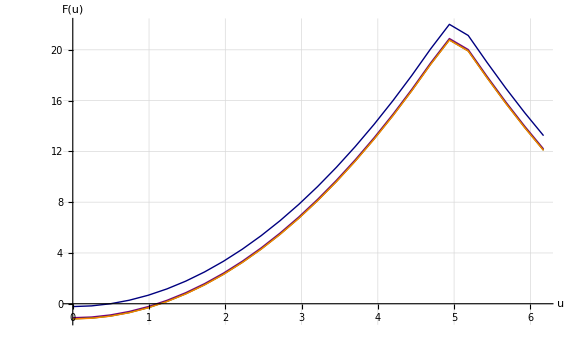

```mathematica
fsAxesLabel=24;
fs2=18;

plot=ListLinePlot[{kappa1,kappa10,kappa50,kappa100},PlotRange->All,ImageSize->Large,GridLines->Automatic,GridLinesStyle->Directive[LightGray,Dashed],AxesLabel->{Style["u",FontSize->fsAxesLabel],Style["F(u)",FontSize->fsAxesLabel]},LabelStyle->{"Times",FontSize->fs2},PlotStyle->{{Thick,Darker[Blue,0.5]},{Thick,Purple},{Thick,Darker[Green,0.6]},{Thick,Orange}},PlotLegend->{Style["κ/κ' = 1",FontSize->fs2],Style["κ/κ' = 10",FontSize->fs2],Style["κ/κ' = 50",FontSize->fs2],Style["κ/κ' = 100",FontSize->fs2]},LegendShadow->None,LegendBorder->None,LegendBackground->Opacity[0],ShadowBackground->Opacity[0],LegendSize->{0.5,0.5},LegendPosition->{0.-0.7,0.0},PlotRange->All]
```

```mathematica
Export["./Intact_kappa_variation_L"<>ToString[L]<>"_m"<>ToString[m]<>"_etab"<>ToString[ηb]<>".pdf",plot]
```

./Intact_kappa_variation_L20_m40_etab0.5.pdf